```mathematica
L=400;(* lattice sites *)
ν=.3;(* filling fraction *)
NF = Floor[ν*L];(* number of particles *)
NF =If[EvenQ[NF],NF+1,NF]
ρ=NF/L;(* average density *)
t=1.0;(* hopping amplitude *) 
usePBC=True; (* PBC yes / no *)
```

121

```mathematica
Ham = ConstantArray[0,{L,L}];
Do[
Ham[[ii,ii+1]]=-t
,{ii,1,L-1}]
If[usePBC,Ham[[1,L]]=-t;]
Ham = Ham + Ham†;
{eval,evec}=Eigensystem[Ham];(* compute the eigensystem *)
order=Ordering[eval];(* bring to ascending order Subscript[E, 1] ≤ Subscript[E, 2] ≤ Subscript[E, 3] ≤ ... *)
eval = eval[[order]];
evec = evec[[order]];
If[DeleteDuplicates[Chop[eval-Diagonal[evec.Ham.evecᵀ],10^-14]][[1]]≠ 0, Print["THIS IS WRONG!"] ](* the transposed eigenvector matrix diagonalizes H *)
gs=evec[[;;NF]];(* modes contributing to the groundstate *)
idx = Join[Table[i,{i,1,NF-1}],{NF+1}]; (* modes contributing to the first excited state *)
fex = evec[[idx]];
obdmGS=gsᵀ.gs;(*the greens function <Subscript[(c†), i] Subscript[c, j]>_GS*)
obdmFEX=fexᵀ.fex;(*the greens function <Subscript[(c†), i] Subscript[c, j]>_(1^st ex.)*)
κinv=ρ^2*( Total[eval[[;;NF+1]]]+Total[eval[[;;NF-1]]]-2*Total[eval[[;;NF]]]) ;(* the inverse compressibility *)
nncorrGS[i_,j_]:=obdmGS[[i,j]]KroneckerDelta[i,j]-obdmGS[[i,j]]*obdmGS[[j,i]]; (* Wick expansion of <Subscript[n, i] Subscript[n, j]>-<Subscript[n, i]><Subscript[n, j]>*)
nncorrFEX[i_,j_]:=obdmFEX[[i,j]]KroneckerDelta[i,j]-obdmFEX[[i,j]]*obdmFEX[[j,i]]; (* Wick expansion of <Subscript[n, i] Subscript[n, j]>-<Subscript[n, i]><Subscript[n, j]>*)
SGS[k_]=1/L*Sum[Exp[ⅈ * k * (x-y)]*nncorrGS[x,y],{x,1,L},{y,1,L}];(* the structure factor *)
SFEX[k_]=1/L*Sum[Exp[ⅈ * k * (x-y)]*nncorrFEX[x,y],{x,1,L},{y,1,L}];(* the structure factor *)
velocity = κinv /π/ρ^2//N; (* formula for the velocity of sound *)
luttingerK = L*S[2π/L];(* the luttinger K from the structure factor *)
Print["luttinger K=", luttingerK]
EFEX=Tr[obdmFEX.Ham];(* energy of the ground state *)
EGS=Tr[obdmGS.Ham];(* energy of the excited state *)
ELS=(EFEX-EGS); (* the level splitting *)
If[!((Tr[obdmGS.Ham])==(eval[[;;NF]]//Total))==((Tr[obdmFEX.Ham])==(eval[[;;NF-1]]//Total)+eval[[NF+1]]),Print["WRONG!"]] (* just a check *)
```

luttinger K=1.+8.67362×10^-19 ⅈ

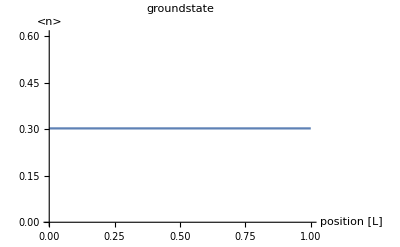

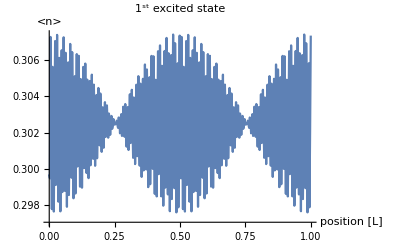

```mathematica
densGS[L]=ListPlot[Diagonal[obdmGS],DataRange->{0,1},Joined->True,AxesLabel->{"position [L]","<n>"},PlotLabel->"groundstate"]
densFEX[L]=ListPlot[Diagonal[obdmFEX],DataRange->{0,1},Joined->True,AxesLabel->{"position [L]","<n>"},PlotLabel->"1^st excited state"]
```

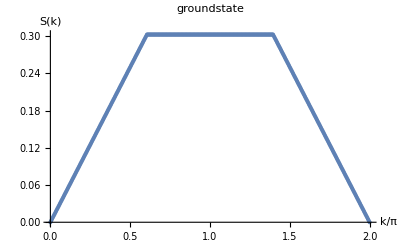

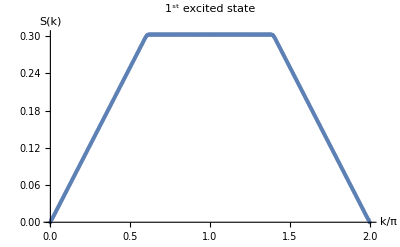

```mathematica
ListPlot[Table[{k/π,SGS[N[k]]},{k,0,2π,2π/L}],PlotRange->Full,AxesLabel->{"k/π","S(k)"},PlotLabel->"groundstate"]
ListPlot[Table[{k/π,SFEX[N[k]]},{k,0,2π,2π/L}],PlotRange->Full,AxesLabel->{"k/π","S(k)"},PlotLabel->"1^st excited state"]
```

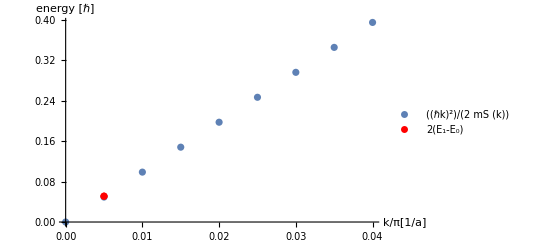

```mathematica
ListPlot[{Table[{k/π,k^2/(2SGS[N[k]])},{k,0,16π/L,If[usePBC,2,1]*π/L}],{{If[usePBC,2,1]/L,2ELS}}},PlotStyle->{Automatic,Red},PlotLegends->Placed[{"(ℏk)^2/(2  mS (k))","2(E_1-E_0)"},{Right,Bottom}],PlotRange->Full,AxesLabel->{"k/π[1/a]","energy [ℏ]"}]
```